```mathematica
k[1]=10;
k[-1]=1;
k[2]=20;
k[3]=10;
k[-3]=1;
k[4]=20;
a[m]=1;
a[p]=10;
funciones={Adh,Ak,F,AdhS[2],F[e],FS[1],S[1],S[2]}; 
soluciones={$Adh,$Ak,$F,$AdhS[2],$F[e],$FS[1],$S[1],$S[2]};

eq1 =F'[t]==-k[1]S[1][t]F[t]+k[-1]FS[1][t]+a[p]F[e][t]-a[m]F[t];
eq2=FS[1]'[t]==k[1]S[1][t]F[t]-(k[2]+k[-1])FS[1][t];
eq3=S[1]'[t]==-k[1]S[1][t]F[t]+(k[2]+k[-1])FS[1][t];
eq4=Adh'[t]==k[2]FS[1][t]-k[3]S[2][t]Adh[t]+k[-3]AdhS[2][t];
eq5=AdhS[2]'[t]==k[3]S[2][t]Adh[t]-(k[4]+k[-3])AdhS[2][t];
eq6 =S[2]'[t]==-k[3]S[2][t]Adh[t]+(k[4]+k[-3])AdhS[2][t];
eq7=Ak'[t]==k[4]Adh[t];
eq8=F[e]'[t]==-a[p]F[e][t]+a[m]F[t];

ecuaciones={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8};


inicial={Adh[0]==0,Ak[0]==0,F[0]==10,AdhS[2][0]==0,F[e][0]==5000,FS[1][0]==0,S[1][0]==10,S[2][0]==10};
soluciones=NDSolveValue[{ecuaciones,inicial},funciones,{t,0,100}];
sol1 = NDSolve[{ecuaciones,inicial},funciones,{t,0,100}]
```

{{Adh→InterpolatingFunction[…],Ak→InterpolatingFunction[…],F→InterpolatingFunction[…],AdhS[2]→InterpolatingFunction[…],F[e]→InterpolatingFunction[…],FS[1]→InterpolatingFunction[…],S[1]→InterpolatingFunction[…],S[2]→InterpolatingFunction[…]}}

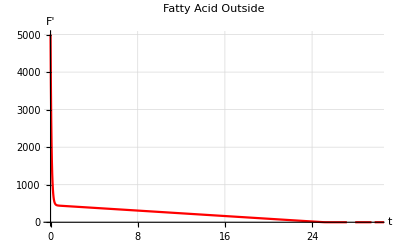

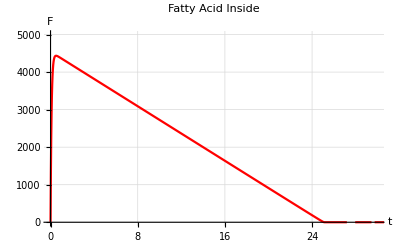

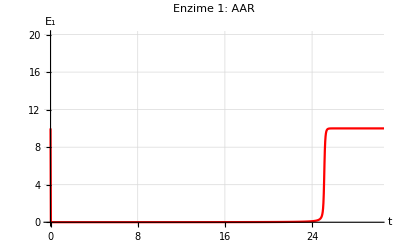

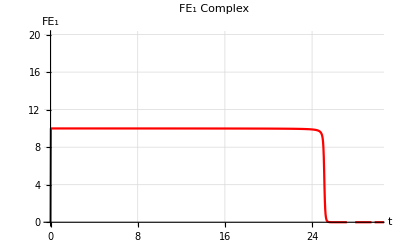

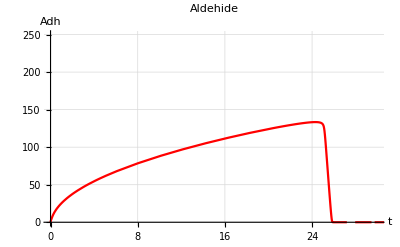

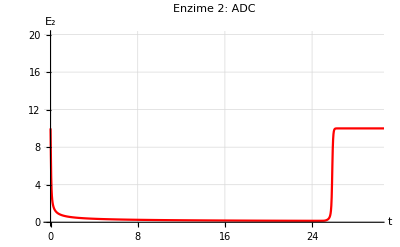

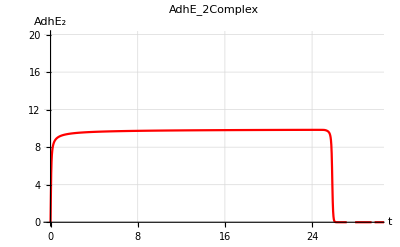

Plot::nonopt: Options expected (instead of Null) beyond position 2 in Plot[{InterpolatingFunction[{{0.,100.}},{5,7,1,{1887},{4},0,0,0,0,Automatic,«3»},{{0.,6.35938×10^-8,1.27188×10^-7,4.07878×10^-6,8.03037×10^-6,«24»,0.0000226256,0.0000332692,0.0000439129,0.0000545565,«1877»}},{Developer`PackedArrayForm,{0,2,4,6,8,10,12,14,16,18,«1878»},{0.,0.,1.02874×10^-16,1.61767×10^-9,4.11587×10^-16,4.85445×10^-9,6.64813×10^-12,3.35972×10^-6,3.91289×10^-11,0.0000130796,«3764»}},{Automatic}][t]},«7»]. An option must be a rule or a list of rules.

Plot[{InterpolatingFunction[…][t]},{t,0,100},GridLines→Automatic,PlotRange→{{0,5},{0,5000}},PlotLabel→Alkane result,PlotStyle→Red,Null,AxesLabel→{t,Ak}]

```mathematica
Plot[Evaluate[F[e][t]/.sol1],{t,0,100},PlotRange->{{0,30},{0,5000}},GridLines->Automatic,PlotLabel->"Fatty Acid Outside", PlotStyle->Red, AxesLabel->{"t","F'"}]
Plot[Evaluate[F[t]/.sol1],{t,0,100},GridLines->Automatic,PlotRange->{{0,30},{0,5000}},PlotLabel->"Fatty Acid Inside", PlotStyle->Red, AxesLabel->{"t","F"}]
Plot[Evaluate[S[1][t]/.sol1],{t,0,100},GridLines->Automatic,PlotRange->{{0,30},{0,20}},PlotLabel->"Enzime 1: AAR", PlotStyle->Red, AxesLabel->{"t","E_1"}]
Plot[Evaluate[FS[1][t]/.sol1],{t,0,100},GridLines->Automatic,PlotRange->{{0,30},{0,20}},PlotLabel->"FE_1 Complex", PlotStyle->Red, AxesLabel->{"t","FE_1"}]
Plot[Evaluate[Adh[t]/.sol1],{t,0,100},GridLines->Automatic,PlotRange->{{0,30},{0,250}},PlotLabel->"Aldehide", PlotStyle->Red, AxesLabel->{"t","Adh"}]
Plot[Evaluate[S[2][t]/.sol1],{t,0,100},GridLines->Automatic,PlotRange->{{0,30},{0,20}},PlotLabel->"Enzime 2: ADC", PlotStyle->Red, AxesLabel->{"t","E_2"}]
Plot[Evaluate[AdhS[2][t]/.sol1],{t,0,100},GridLines->Automatic,PlotRange->{{0,30},{0,20}},PlotLabel -> "AdhE_2Complex", PlotStyle->Red, AxesLabel->{"t","AdhE_2"}]
Plot[Evaluate[Ak[t]/.sol1],{t,0,100},GridLines->Automatic,PlotRange->{{0,5},{0,5000}},PlotLabel->"Alkane result", PlotStyle->Red,, AxesLabel->{"t","Ak"}]
```